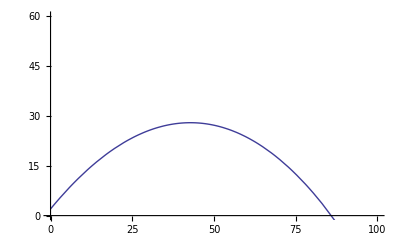

```mathematica
g = 9.8 (*m/s^2*);
v =30;
vt=100;
θ=50 π/180;

ode1 ={x''[t]==(-g x'[t]/ vt^2) Sqrt[x'[t]^2 + y'[t]^2], y''[t]==-g(1+(y'[t]/vt^2) Sqrt[x'[t]^2+y'[t]^2]), x[0]==0,y[0]==2, x'[0]== v*Cos[θ], y'[0]==v*Sin[θ]};
sol=NDSolve[{x''[t]==(-g x'[t]/ vt^2) Sqrt[x'[t]^2 + y'[t]^2], y''[t]==-g(1+(y'[t]/vt^2) Sqrt[x'[t]^2+y'[t]^2]), x[0]==0,y[0]==2, x'[0]== v*Cos[θ], y'[0]==v*Sin[θ]}, {x,y},{t,0,200}];
ParametricPlot[Evaluate[
{x[t],y[t]}/.sol],
 {t, 0, 60}, PlotRange->{{0,100},{0,60}}]

Manipulate [ParametricPlot[Evaluate[
{x[t],y[t], v Cos[θ]t,z+v  Sin[θ]t-4.9t^2}/.
NDSolve[{x''[t]==(-g x'[t]/ vt^2) Sqrt[x'[t]^2 + y'[t]^2], y''[t]==-g(1+(y'[t]/vt^2) Sqrt[x'[t]^2+y'[t]^2]), x[0]==0,y[0]==h, x'[0]== v*Cos[θ], y'[0]==v*Sin[θ]}, {x,y},{t,0,200}]],
 {t, 0, tf}, PlotRange->{{0,4000},{-10,200}}],
{{tf,0.01,"time(s)"},0.01,30, Appearance->"Labeled"}, 
{{v,10,"Velocity(m/s)"},0.01,439, 
Appearance->"Labeled"},
{{g,9.8,"Gravity(m/s^s"}, 0.01,4*9.8, 
Appearance->"Labeled"},
{{vt, 10, "Terminal Velocity(m/s)"}, 1.0, 135,
 Appearance->"Labeled"},
{{h, 0, "Starting Height(m)"}, 0.0, 5, 
Appearance->"Labeled"},
{{θ,50 Pi/180,"θ(rad/s)"},0.01,π /2, 
Appearance->"Labeled"}]
```

2.
a.
Projectile | Velocity(m/s) | Angle(rad) | Velocity without air resistance(m/s) | Angle with no air resistance(rad)
Human Cannonball | 31 | .909019 | 28 | .905897
Golf Ball | 37 | 1.03388 | 29 | .974572
Baseball | 41 | 1.12441 | 30 | 1.05261

b. Civil war Cannon ball
Angle(degreees) | Range(m)
5 | 1760
10 | 2385
15 | 2775

c.
within range of 1000 meters
Angle(degrees) | Velocity(m/s)
5 | <260
10 | <210
15 | <166